#### Set plot styles and custom plot functions

```mathematica
SetOptions[#,Frame->True,FrameStyle->Directive[Black,18,FontFamily->Times,Thickness[.004]],AspectRatio->1,PlotStyle->Thick,ImageSize->400]&@{Plot,LogPlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot};
SetOptions[#,Frame->True,LabelStyle->Directive[Black,16,FontFamily->Times,Thickness[.004]],AspectRatio->1,ImageSize->400]&@{Histogram,MatrixPlot};
logSpace[a_, b_, n_] := 10.0^Range[Log10[a], Log10[b], (Log10[b] - Log10[a])/(n - 1)];

topLeft[x_] := Placed[x, {Scaled[{.38, .95}], {.9, 1}}];
topRight[x_] := Placed[x,{Scaled[{.95, .95}], {.9, 1}}];
Legend//Clear;
Legend[legendList_,opt:OptionsPattern[{Position->"Right",Type->"Line",LineLegend}]] := Module[{f},
If[OptionValue[Type]=="Line",
f=LineLegend;];
If[OptionValue[Type]=="Swatch",
f=SwatchLegend;];
If[OptionValue[Position]=="Right",
f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//topRight//Return];
If[OptionValue[Position]=="Left",
f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//topLeft//Return];
f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//Placed[#,OptionValue[Position]]&//Return;
];
LogTicks//Clear;
LogTicks[min_,max_,step_] := Block[{lmin, lmax, t},
   lmin = Floor[Log10[min]];
   lmax = Floor[Log10[max]];
   t=0;
   Return[{Join[
      Table[{10^i, If[Mod[++t,step]==0,Superscript[10, i],Null], {0.012, 0}}, {i, Floor[lmin], Ceiling[lmax]}], (Flatten[#1, 1] &)[
       Table[{i*10^j, Null, {0.006, 0}}, {j, Floor[lmin], 
        Ceiling[lmax], 1}, {i, 0.1, 0.9, 0.1}]]], 
     Join[Table[{10^i, Null, {0.012, 0}}, {i, Floor[lmin], 
     Ceiling[lmax]}], (Flatten[#1, 1] &)[ Table[{i*10^j, Null, {0.006, 0}}, {j, Floor[lmin], Ceiling[lmax], 1}, {i, 0.1, 0.9, 0.1}]]]}  ]
];
LogTicks[min_, max_] := LogTicks[min,max,1];
```

## Constants

```mathematica
eV=10^-9;
keV=10^-6;
MeV=10^-3;
GeV=1;
ℏcGeVfm=0.19732698;(*GeV fm*)
𝒸=2.997925 10^8;(*m/s*)

e=0.30282212;
Gf=1.1664 10^-5;(*GeV^-2*)
gA=1.26;
```

Other useful units:

```mathematica
Centimeter= 1/ℏcGeVfm 10^13(*GeV^-1*);
```

```mathematica
Ar40={"Ar",18,40,0,"ar40_s.res"};
Nucleus=Ar40;


mN=0.938;
mA=Nucleus⟦3⟧ mN;
Ji=Nucleus⟦4⟧;
qVp=0.01556533;
qVn=-0.5122125;
b[A_]:=√(41.467/(45 A^(-1/3)-25 A^(-2/3)));
yy[q_,A_]:= ((q b[A])/(2ℏ𝒸))^2;
```

## Calculate cross sections

### Define GT cross section

a factor of 2 is conventional

```mathematica
σGT[Enu_,ω_,BGT_]:=(2 Gf^2 gA^2)/(π(2Ji+1))(Enu-ω)^2 BGT UnitStep[Enu-ω]
```

### Argon

Import strengths:

```mathematica
NotebookDirectory[]//SetDirectory;
```

```mathematica
nuclStrengths=Import[Nucleus⟦5⟧,"Table"][[10;;509]];
```

Shift to relative energies and convert to GeV:

```mathematica
nuclStrengths[[All,1]]-=nuclStrengths[[1,1]];
nuclStrengths[[All,1]]*=MeV;
```

First 20 non-zero transitions:

```mathematica
nuclStrengthsNon0=nuclStrengths//DeleteCases[#,_?(#[[2]]==0&)]&;nuclStrengthsNon0[[1;;20]]//MatrixForm
(*energy in GeV, strength function*)
```

(0.00325988 | 0.06583
0.004639 | 0.00058
0.00524681 | 0.00277
0.00585763 | 0.00075
0.0086381 | 0.00007
0.00925304 | 0.00979
0.00994599 | 0.0177
0.0101513 | 0.02626
0.0108052 | 0.002
0.0110938 | 0.00377
0.0114019 | 0.01938
0.0115691 | 0.39735
0.011787 | 0.03552
0.0118216 | 0.00539
0.012356 | 0.01451
0.0124792 | 0.01051
0.0127116 | 0.02327
0.0128182 | 0.00791
0.0128567 | 0.18201
0.0131314 | 0.00215)

Plot strengths:

Calculate cross sections:

```mathematica
nuclGTcs=Table[{10^3 nuclStrengthsNon0[[ii,1]],σGT[30MeV,nuclStrengthsNon0[[ii,1]],nuclStrengthsNon0[[ii,2]]] Centimeter^-2},{ii,1,Length[nuclStrengthsNon0]}];
```

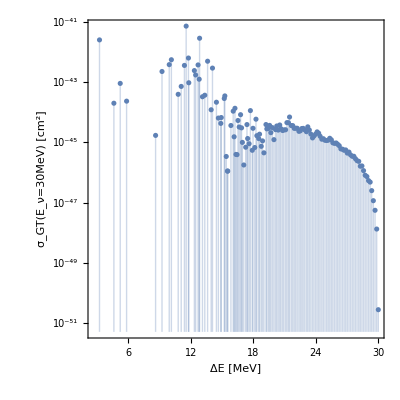

```mathematica
ListLogPlot[nuclGTcs,Filling->Bottom,FrameLabel->{"ΔE [MeV]","σ_GT(E_ν=30MeV) [cm^2]"},PlotRange->All]
```

Total cross section:

```mathematica
nuclGTtotalCS=Table[{Enu,
Plus@@Table[σGT[Enu MeV,nuclStrengthsNon0[[ii,1]],nuclStrengthsNon0[[ii,2]]] Centimeter^-2 10^42,{ii,1,Length[nuclStrengthsNon0]}]},{Enu,1,100}];
```

```mathematica
σGTEν[Enu_]:= Sum[σGT[Enu,nuclStrengthsNon0[[ii,1]],nuclStrengthsNon0[[ii,2]]],{ii,1,Length[nuclStrengthsNon0]}];
```

### Elastic

```mathematica
FHelm[A_,Er_]:=3(Sin[q r]-(q r)Cos[q r])/(q r)^3 Exp[(-(q s)^2)/2]/.{q->6.92*10^-3 √A √Er,r->((1.23 A^(1/3)-.6)^2+7/3 π^2(0.52)^2-5(0.9)^2)^(1/2),s->0.9}
dσdErHi[ErkeV_,EnuMeV_]:=(Gf^2(Nucleus⟦3⟧ mN))/(2π)(1+(1-ErkeV/(EnuMeV 10^3))^2-(Nucleus⟦3⟧ mN ErkeV)/EnuMeV^2)(Nucleus⟦2⟧ qVp+(Nucleus⟦3⟧-Nucleus⟦2⟧) qVn)^2 FHelm[Nucleus⟦3⟧,ErkeV]^2;
σHi[EnuMeV_]:=10^-6 NIntegrate[dσdErHi[Er,EnuMeV],{Er,0,(2 EnuMeV^2 10^6)/(mA 10^6+2 10^3 EnuMeV)}];
pointsEl=Table[{EnuMeV,10^42 Centimeter^-2 σHi[EnuMeV]},{EnuMeV,1,100}];
```

### Plot

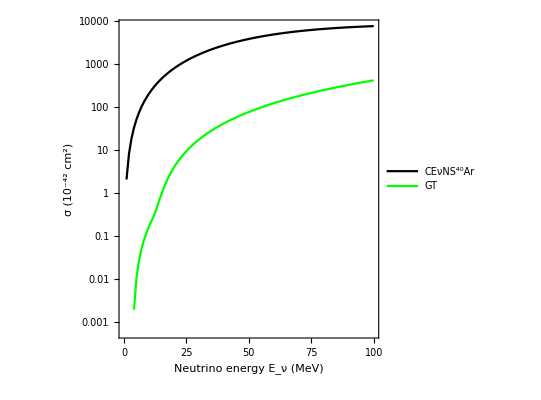

```mathematica
ListLogPlot[{pointsEl,nuclGTtotalCS},Joined->True,PlotStyle->{Black,Green},PlotLegends->Legend[{"CEνNS^40Ar","GT"},Position->{0.8,0.13},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Black]&)],FrameLabel->{"Neutrino energy E_ν (MeV)", "σ (10^-42 cm^2)"},FrameTicks->{LogTicks[10^-6,10^6,2],Automatic}]
```

```mathematica
(*Export["ar40_nu_el.csv",pointsEl];
Export["ar40_nu_inel.csv", nuclGTtotalCS];*)
```

## Neutrino flux

### Detector specs

```mathematica
Subscript[N, A]=6 10^23;
yearsCsI=1.61;
yearsLAr=0.6;
yearsCCM=3;

massCsI=14.6;(*kg*)
massLAr=24.4;
massCCM=7000;

DistanceCsI=19.3 10^2; (*cm*)
DistanceLAr=28.4 10^2;
DistanceCCM=20 10^2;

pionRatioCOHERENT=0.0803;
pionRatioCCM=0.052;

POTCsI=3.2 10^23; (*total*)
POTLAr=1.34 10^23;
POTCCM=10^22*yearsCCM;

secCsI=yearsCsI*365*24*60^2;
secLAr=yearsLAr*365*24*60^2;
secCCM=yearsCCM*365*24*60^2;

(*cm^-2 s^-1*)
FluxCsI=POTCsI pionRatioCOHERENT  / (4π DistanceCsI^2 secCsI);
FluxLAr=POTLAr pionRatioCOHERENT / (4π DistanceLAr^2 secLAr) ;
FluxCCM=POTCCM pionRatioCCM / (4π DistanceCCM^2 secCCM) ;

ExposureCsI=massCsI yearsCsI*365; (*kg days*)
ExposureLAr=massLAr yearsLAr*365;
ExposureCCM=massCCM yearsCCM*365;
```

```mathematica
ExposureCCM
FluxCCM
```

7665000

328040.

### Neutrino energy distribution

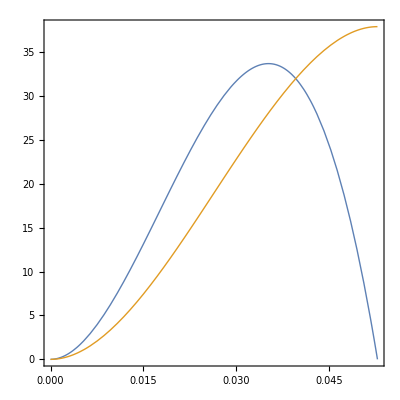

```mathematica
mπ=0.139;
mμ=0.1056;
Epromptν=(mπ^2-mμ^2)/(2mπ);
dPdEνμ[Enu_]:=64/mμ^3 Enu^2(3/4-Enu/mμ); 
dPdEνe[Enu_]:=192/mμ^3 Enu^2(1/2-Enu/mμ); 
Plot[{dPdEνe[Enu],dPdEνμ[Enu]},{Enu,0,mμ/2}]
```

### Neutrino Rate (total event number) at COHERENT LAr and CCM

```mathematica
prefactorLAr=ExposureLAr(10^3 Subscript[N, A])/Nucleus⟦3⟧60^2*24 FluxLAr Centimeter^-2;
prefactorCCM=ExposureCCM(10^3 Subscript[N, A])/Nucleus⟦3⟧60^2*24 FluxCCM Centimeter^-2;

RateElp=σHi[Epromptν 10^3]; (*σHi takes Enu in MeV*)
RateEld= NIntegrate[σHi[Enu 10^3](dPdEνμ[Enu]+dPdEνe[Enu]),{Enu,0,mμ/2}];
RateEl=prefactorLAr(RateElp+RateEld);

RateInelp=σGTEν[Epromptν];
RateIneld=NIntegrate[σGTEν[Enu] (dPdEνμ[Enu]+dPdEνe[Enu]),{Enu,0,mμ/2}];
RateInel=prefactorLAr(RateInelp+RateIneld);
```

NIntegrate::nlim: Er = (2.×10^12 Enu^2)/(3.752×10^7+2.×10^6 Enu) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate`SymbolicPiecewiseSubdivision::maxpwc: The number of piecewise regions has exceeded the maximum value specified by the option MaxPiecewiseCases -> 100. The integration will continue with no piecewise subdivision.

LAr rate

```mathematica
RateEl
RateInel
```

227.678

0.6254

CCM rate

```mathematica
RateEl prefactorCCM/prefactorLAr
RateInel prefactorCCM/prefactorLAr
```

19094.6

52.4502